#### Code Force on a single particle

```mathematica
SingleParticleNewtonianForce[state_,masses_,i_]:=Module[{j,x1,x2,y1,y2,m1,m2,distance2,jforce,jforcedir,forces,Nparticles},
	Nparticles = Length[state];
	forces = Table[{0.,0.},Nparticles];
	x1 = state[[i,1,1]];
	y1 = state[[i,1,2]];
	m1 = masses[[i,1]];
	For [j=1,j<= Nparticles,j++,
		If[j!= i,
			m2 = masses[[j,1]];
			x2 = state[[j,1,1]];
			y2 = state[[j,1,2]];
			distance2 = ((x2-x1)^2+(y2-y1)^2);
			jforce = (m2)/distance2;
			jforcedir = {x2-x1,y2-y1}/Sqrt[distance2];
			forces[[j]] = jforce*jforcedir;
		];
	];
	Return[Total[forces]];
]
```

#### Get force on every particle

GetForces[state_] iterates through the particles in state, passing them through SingleParticleNewtonianForce to return an array of length Nparticles which has the acceleration for every particle, with form {{xdd1,ydd1},...,{xddn,yddn}}.

```mathematica
GetForces[state_,masses_]:=Module[{particle,totalforces,Nparticles},
Nparticles = Length[state];
totalforces = Table[{},Nparticles];
For[particle=1,particle≤Nparticles,particle++,
totalforces[[particle]]=SingleParticleNewtonianForce[state,masses,particle]
];
Return[totalforces]
]
```

#### Time evolution

Pretty straightforward. Solves kinematic equations to time evolve the system.

```mathematica
TimeEvolve[InitVecs_,masses_,timesteps_,dt_]:=Module[{StateVecs,timestep,currentforces,NewState,Nparticles,oldx,oldy,oldxd,oldyd,xdd,ydd,newx,newy,newxd,newyd,m,i,wholestory},
Nparticles=Length[InitVecs];
StateVecs = InitVecs;
wholestory= Table[0,timesteps];
For[timestep = 1,timestep≤timesteps,timestep++,
currentforces = GetForces[StateVecs,masses];
NewState = Table[{{0,0},{0,0}},Nparticles];
For[i=1,i≤ Nparticles,i++,
oldx = StateVecs[[i,1,1]];
oldy = StateVecs[[i,1,2]];
oldxd = StateVecs[[i,2,1]];
oldyd = StateVecs[[i,2,2]];
xdd= currentforces[[i,1]];
ydd = currentforces[[i,2]];
newx = oldxd * dt + oldx;
newy = oldyd * dt + oldy;
newxd = xdd*dt + oldxd;
newyd = ydd*dt + oldyd;
m = StateVecs[[i,1,1]];
NewState[[i,1,1]] = newx;
NewState[[i,1,2]] = newy;
NewState[[i,2,1]] = newxd;
NewState[[i,2,2]] = newyd;
];
StateVecs = NewState;
wholestory[[timestep]] = StateVecs;
];
Return[wholestory]
]
```

#### Test cases Two Particles

#### Initialize the stuff

```mathematica
TwoParticleState = {{{1,0},{0,0.3}},{{-1,0},{0,-.3}}};
TwoParticleNsteps = 100000;
TwoParticledt = 0.0001;
TwoParticleMasses = {{1},{1}};
```

#### Sanity check

For a sanity check, if Nparticles==2, the two forces returned should be equal and opposite.

```mathematica
GetForces[TwoParticleState,TwoParticleMasses]
```

{{-0.25,0.},{0.25,0.}}

#### Do the thing

```mathematica
TwoParticleTrajectories = TimeEvolve[TwoParticleState,TwoParticleMasses,TwoParticleNsteps,TwoParticledt];
```

#### Plotting

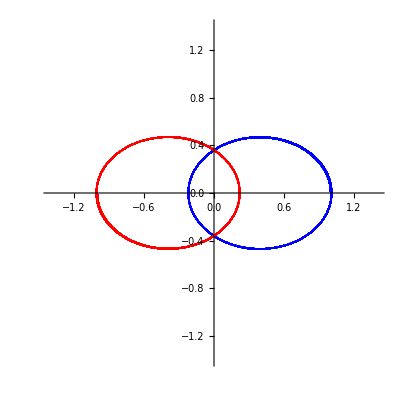

```mathematica
colors= {Blue,Red,Black,Orange,Green};
pltrng=1.4;
xyplot1 = ListPlot[Table[{TwoParticleTrajectories[[i,1,1,1]],TwoParticleTrajectories[[i,1,1,2]]},{i,1,TwoParticleNsteps}],PlotRange->{{-pltrng,pltrng},{-pltrng,pltrng}},PlotStyle->{colors[[1]]},AspectRatio->1];
xyplot2 = ListPlot[Table[{TwoParticleTrajectories[[i,2,1,1]],TwoParticleTrajectories[[i,2,1,2]]},{i,1,TwoParticleNsteps}],PlotRange->{{-pltrng,pltrng},{-pltrng,pltrng}},PlotStyle->{colors[[2]]},AspectRatio->1];
Show[{xyplot1,xyplot2}]
```